```mathematica
ClearAll["Global`*"];

Sol[Q_, L_, Nc_]:=Module[{},

(* ------------------------------------------------------- *)

(* verifica sulla dimensione del sistema *)
check0 = Length[Q]==Length[L] && Length[Q]==Nc && Length[L]==Nc;
If[check0==True,
Print["Le dimensioni degli elementi sono compatibili"],
Print[Style["Le dimensioni degli elementi non sono compatibili. Ricontrollare", FontColor->Red]]
];

(* vettore dei momenti incogniti (positivi per fibre tese all'intradosso) *)
M=Array[m, Nc+1]; 

(* SOLUZIONE DEL SISTEMA LINEARE *)

{R, K} = CoefficientArrays[
Append[
Append[
Table[
M[[i]]*L[[i]]/(6*EJ)+M[[i+1]]*L[[i]]/(3*EJ)+Q[[i]]*L[[i]]^3/(24*EJ)+M[[i+1]]*L[[i+1]]/(3*EJ)+Q[[i+1]]*L[[i+1]]^3/(24*EJ)+M[[i+2]]*L[[i+1]]/(6*EJ)==0,
{i, 1, Nc-1}], M[[1]]==0],Last[M]==0],
Table[m[i], {i, 1, Nc+1}]]//Normal;
R = -R;
MatrixForm[K];
MatrixForm[R];
MatrixForm[M];

M = LinearSolve[K, R]//FullSimplify;
Print["M = ",MatrixForm[M]];

(*M = M/.Solve[M.K-R==0, M][[1]];*)


(* Reazioni vincolari (positive verso l'alto) *)

V = Array[v, Nc+1];
{RV, MV} = CoefficientArrays[
 Append[
Prepend[
Table[V[[i]]==(M[[i-1]]-M[[i]])/L[[i-1]]-(M[[i]]-M[[i+1]])/L[[i]]+1/2*(Q[[i-1]]*L[[i-1]]+Q[[i]]*L[[i]]), {i, 2, Nc}
],
Table[V[[j]]==1/2*Q[[j]]*L[[j]]-(M[[j]]-M[[j+1]])/L[[j]], {j, 1,1}][[1]]
],
Table[V[[j]]==1/2*Q[[j]]*L[[j]]+(M[[j]]-M[[j+1]])/L[[j]], {j, Nc,Nc}][[1]]
],
Table[V[[i]], {i, 1, Nc+1}]
]//Normal//Simplify;
RV = -RV;
Print["R_V = ", MatrixForm[RV]];


(* verifica equilibrio alla traslazione verticale *)

check = Sum[RV[[i]], {i, 1, Length[RV]}]-Sum[Q[[i]]*L[[i]], {i, 1, Length[Q]}]//FullSimplify;
If[check == 0, 
Print[Style["Equilibrio alla traslazione verticale soddisfatto", FontColor->Automatic]], 
Print[Style["Equilibrio alla traslazione verticale soddisfatto", FontColor->Red]]]

]
```

```mathematica
(* numero di campate. Inserire il valore numerico *)
Nc = 10;

(* vettore dei carichi trasversali distribuiti. Inserire il valore numerico *)
Q0 = {1,1,0,0,0,0,0,0,0,0};
Q= {5,5,5,5,5,5,5,5,5,5};
(* vettore delle lunghezze delle campate. Inserire il valore numerico *)
L= {5,5,5,5,5,5,5,5,5,5};

Sol[Q0,L,Nc]
```

Le dimensioni degli elementi sono compatibili

M = (0
-877825/302632
-33950/37829
72775/302632
-4875/75658
25/1448
-175/37829
375/302632
-25/75658
25/302632
0)

R_V = (581015/302632
904985/151316
352105/151316
-43665/151316
2925/37829
-15/724
210/37829
-225/151316
15/37829
-15/151316
5/302632)

Equilibrio alla traslazione verticale soddisfatto

```mathematica
M//N//MatrixForm
```

(0.
-2.90064
-0.89746
0.240474
-0.0644347
0.0172652
-0.00462608
0.00123913
-0.000330434
0.0000826086
0.)

```mathematica
L0= Append[L*0,0];
For[i=2, i<Nc+2, i++,
L0[[i]]= L0[[i-1]]+L[[i-1]];
]
L0
Ltot = Last[L0];
```

{0,5,10,15,20,25,30,35,40,45,50}

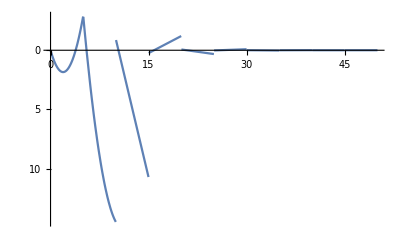

```mathematica
Plot[
Sum[(M[[i]]+RV[[i]]*(s-L0[[i]])-Q0[[i]]*(s-L0[[i]])^2/2)*(HeavisideTheta[s-L0[[i]]]-HeavisideTheta[s-L0[[i+1]]]),
{i, 1, Nc}],
{s, L0[[1]], Last[L0]},
ScalingFunctions->"Reverse",
PlotRange->Full
]
```